=== Starting computation ===

Setup: 0. seconds

Landmarks computation: 0.020316 seconds

Computing derivatives (61 total)...

Derivative 0/60 took 0.1817042 seconds (3 roots, degRaw=90)

Derivative 5/60 took 0.2262779 seconds (18 roots, degRaw=90)

Derivative 10/60 took 0.3905281 seconds (33 roots, degRaw=90)

Derivative 15/60 took 0.6308541 seconds (48 roots, degRaw=90)

Derivative 20/60 took 0.8724844 seconds (63 roots, degRaw=90)

Derivative 25/60 took 1.2960148 seconds (78 roots, degRaw=90)

Derivative 30/60 took 1.7184427 seconds (90 roots, degRaw=90)

Derivative 35/60 took 1.8826444 seconds (90 roots, degRaw=90)

Derivative 40/60 took 1.9861519 seconds (90 roots, degRaw=90)

Derivative 45/60 took 2.1025170 seconds (90 roots, degRaw=90)

Derivative 50/60 took 2.2713439 seconds (90 roots, degRaw=90)

Derivative 55/60 took 2.4003726 seconds (90 roots, degRaw=90)

Derivative 60/60 took 2.4803000 seconds (90 roots, degRaw=90)

Total derivatives computation: 86.4724973 seconds

Root concatenation: 0.024712 seconds

Total roots collected: 4185

Computing FF polynomial...

FF computation: 0. seconds

Computing resultant...

Resultant computation: 0.0575459 seconds

Solving resultant for 399 alpha values...

Alpha step 100/399 (α=1.), time: 0.0060082 s

Alpha step 200/399 (α=2.), time: 0.0060656 s

Alpha step 300/399 (α=3.), time: 0.0060185 s

Alpha step 399/399 (α=3.99), time: 0.0060097 s

Total resultant solving: 2.531016 seconds

Resultant roots found: 3986

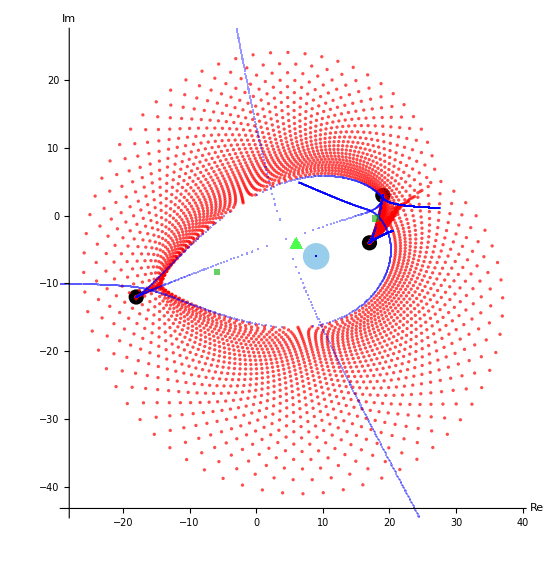

Plot creation: 0.428081 seconds

Export: 2.919869 seconds

=== Total time: 92.4611917 seconds ===

```mathematica
ClearAll["Global`*"];
$HistoryLength=0;

n=30;
resStepLength=1/100;

Print["=== Starting computation ==="];
startTime=AbsoluteTime[];

t1=AbsoluteTime[];
z;w;

P=(z-(19+3 I)) (z-(17-4 I)) (z-(-18-12 I));
Q=(z-(9-6 I)) (z-(5+6 I));
R=P/Q;

dP=Exponent[P,z];
dQ=Exponent[Q,z];
d=dP+dQ;
maxDerivOrder=(dP-dQ) n;  (* IMPORTANT: m<=(dP-dQ) n*)

precision=Max[80,10 d+2 n];
resPrecision=precision;
$MaxExtraPrecision=50;

Print["Setup: ",AbsoluteTime[]-t1," seconds"];


ClearAll[FiniteNumericQ];
FiniteNumericQ[x_]:=NumericQ[x]&&FreeQ[N[x],_DirectedInfinity|_ComplexInfinity|Indeterminate];

ClearAll[CleanPairs];
CleanPairs[pts_]:=Module[{p=N[pts]//Chop},Select[p,MatchQ[#,{_,_}]&&And@@(NumericQ/@#)&&FreeQ[#,_DirectedInfinity|_ComplexInfinity|Indeterminate]&]];

ClearAll[SafeBounds];
SafeBounds[pts_,padFrac_:1/30]:=Module[{xs,ys,xmin,xmax,ymin,ymax,span,pad},If[!ListQ[pts]||Length[pts]==0,Return[None]];
xs=pts[[All,1]];ys=pts[[All,2]];
If[!VectorQ[xs,NumericQ]||!VectorQ[ys,NumericQ],Return[None]];
{xmin,xmax}=MinMax[xs];{ymin,ymax}=MinMax[ys];
If[!And@@(FiniteNumericQ/@{xmin,xmax,ymin,ymax}),Return[None]];
span=Max[xmax-xmin,ymax-ymin];
pad=padFrac*If[span<=0,1,span];
{xmin-pad,xmax+pad,ymin-pad,ymax+pad}];

ClearAll[SquareFreePart];
SquareFreePart[poly_,var_Symbol]:=Module[{g},g=PolynomialGCD[poly,D[poly,var]];
If[g===0||g===1,Expand[poly],Expand[Together[poly/g]]]];

ClearAll[Roots2D];
Roots2D[poly_,var_Symbol,wp_Integer:resPrecision,tlim_:15]:=Module[{polySF,deg,polyN,rules,res},polySF=SquareFreePart[poly,var];
deg=Exponent[polySF,var];
If[deg<1,Return[{}]];
polyN=SetPrecision[Expand[polySF],wp];
res=Quiet@Check[TimeConstrained[rules=NRoots[polyN==0,var,WorkingPrecision->wp];
ReIm[var]/. rules//N//Chop,tlim],$Failed];
If[res===$Failed||res==={},polyN=SetPrecision[Expand[polySF],Max[50,wp-10]];
res=Quiet@Check[TimeConstrained[rules=NRoots[polyN==0,var,WorkingPrecision->Max[50,wp-10]];
ReIm[var]/. rules//N//Chop,Max[6,Round[tlim/2]]],{}];
If[res==={},res=Quiet@Check[TimeConstrained[ReIm[var]/. NSolve[polyN==0,var,WorkingPrecision->Max[50,wp-10]],3],{}];];];
CleanPairs[res]];

ClearAll[DerivNumerator];
DerivNumerator[m_Integer?NonNegative]:=Module[{expr},expr=D[(P/Q)^n,{z,m}];
Numerator[Together[expr]]];

t2=AbsoluteTime[];
rootsOfP=ReIm[z]/. Quiet@NSolve[P==0,z,WorkingPrecision->precision]//N//Chop//CleanPairs;
rootsOfQ=ReIm[z]/. Quiet@NSolve[Q==0,z,WorkingPrecision->precision]//N//Chop//CleanPairs;
rootsOfPPrime=ReIm[z]/. Quiet@NSolve[D[P,z]==0,z,WorkingPrecision->precision]//N//Chop//CleanPairs;
centerOfMassOfZP=If[Length[rootsOfP]>=1,Mean[rootsOfP],{0.,0.}];
Print["Landmarks computation: ",AbsoluteTime[]-t2," seconds"];

(* Zeros of derivatives of R^n up to (dP-dQ)n *)
t3=AbsoluteTime[];
Print["Computing derivatives (",maxDerivOrder+1," total)..."];

rootsByDerivative=Table[Module[{tDeriv=AbsoluteTime[],num,degRaw,roots={}},num=DerivNumerator[m];
degRaw=Exponent[num,z];
roots=Roots2D[num,z,resPrecision,20];
If[Mod[m,5]==0||m==maxDerivOrder,Print["  Derivative ",m,"/",maxDerivOrder," took ",NumberForm[AbsoluteTime[]-tDeriv,{Infinity,7}]," seconds (",Length[roots]," roots, degRaw=",degRaw,")"]];
roots],{m,0,maxDerivOrder}];

Print["Total derivatives computation: ",AbsoluteTime[]-t3," seconds"];

t4=AbsoluteTime[];
allRoots=CleanPairs[Join@@rootsByDerivative];
Print["Root concatenation: ",AbsoluteTime[]-t4," seconds"];
Print["Total roots collected: ",Length[allRoots]];

t5=AbsoluteTime[];
Print["Computing FF polynomial..."];
FF=Sum[Sum[((α+j-2 k)/((j-k)! k!))*D[P,{z,k}]*D[Q,{z,j-k}]*w^(d-j),{k,0,j}],{j,0,d}];
Print["FF computation: ",AbsoluteTime[]-t5," seconds"];

t6=AbsoluteTime[];
Print["Computing resultant..."];
RES=Resultant[FF,D[FF,w],w];
Print["Resultant computation: ",AbsoluteTime[]-t6," seconds"];

t7=AbsoluteTime[];
alphaSteps=Length[Range[0+resStepLength,d-resStepLength,resStepLength]];
Print["Solving resultant for ",alphaSteps," alpha values..."];

resultantRoots={};
counter=0;
Do[Module[{tAlpha=AbsoluteTime[],rootsAttempt={},RESz,RESzSF},counter++;
RESz=RES/. α->αVal;
If[Exponent[RESz,z]>=1,RESzSF=SquareFreePart[RESz,z];
rootsAttempt=Roots2D[RESzSF,z,resPrecision,6];
If[rootsAttempt=!={},resultantRoots=Join[resultantRoots,rootsAttempt]];];
If[Mod[counter,100]==0||counter==alphaSteps,Print["  Alpha step ",counter,"/",alphaSteps," (α=",N[αVal,3],"), time: ",NumberForm[AbsoluteTime[]-tAlpha,{Infinity,7}]," s"]];],{αVal,0+resStepLength,d-resStepLength,resStepLength}];

resultantRoots=CleanPairs[resultantRoots];
Print["Total resultant solving: ",AbsoluteTime[]-t7," seconds"];
Print["Resultant roots found: ",Length[resultantRoots]];

t8=AbsoluteTime[];

landmarksCloud=Join[rootsOfP,rootsOfQ,rootsOfPPrime]//CleanPairs;
primaryCloud=If[allRoots=!={},allRoots,landmarksCloud]//CleanPairs;

bounds=SafeBounds[primaryCloud];
If[bounds===None,Print["[warn] No finite points found to bound the plot; using safe defaults."];
bounds={-10.,10.,-10.,10.};];

{xmin,xmax,ymin,ymax}=bounds;

convHullDims=If[primaryCloud==={},{1.,1.},(Max[#]-Min[#]&/@Transpose[primaryCloud])];
pad=Max[convHullDims]/30.;
rectSize=Max[convHullDims]/800.;
critPointsRectSize=Max[convHullDims]/150.;
s=Max[convHullDims]/35.;
rootRadius=Max[0.0015,(14054-Length[allRoots])/2265000.];

axesOriginValue=If[And@@(FiniteNumericQ/@{xmin,ymin}),{xmin,ymin},Automatic];

finalPlot=Graphics[{{Black,PointSize[.02],Point[rootsOfP]},{RGBColor[152/255.,206/255.,235/255.],PointSize[.035],Point[rootsOfQ]},{Opacity[0.7],Red,PointSize[rootRadius],Point[allRoots]},{Opacity[0.4],Blue,PointSize[.0015],Rectangle[#-rectSize,#+rectSize]&/@resultantRoots},{Opacity[0.6],RGBColor[0,175/255.,0],PointSize[.001],Rectangle[#-critPointsRectSize,#+critPointsRectSize]&/@rootsOfPPrime},{Opacity[0.7],RGBColor[0,1,0],PointSize[.0015],With[{c=centerOfMassOfZP},Triangle[{{c[[1]],c[[2]]+s/Sqrt[3]},{c[[1]]-s/2,c[[2]]-s/(2 Sqrt[3])},{c[[1]]+s/2,c[[2]]-s/(2 Sqrt[3])}}]]}},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->Automatic,PlotRange->{{xmin,xmax},{ymin,ymax}},AxesOrigin->axesOriginValue]

Print["Plot creation: ",AbsoluteTime[]-t8," seconds"];

t9=AbsoluteTime[];
base=StringJoin["RationalShadow-n",ToString[n]];
Export[base<>".pdf",finalPlot];
Export[base<>".png",finalPlot,ImageSize->2048];
Export[base<>".eps",finalPlot];
Print["Export: ",AbsoluteTime[]-t9," seconds"];

Print["=== Total time: ",AbsoluteTime[]-startTime," seconds ==="];
```